# 3D 环

## 旋转形式

```mathematica
RevolutionPlot3D[{2+Cos[t],Sin[t]},{t,0,2Pi}]
```

-Graphics3D-

```mathematica
Manipulate[RevolutionPlot3D[{2+Cos[t],Sin[t]},{t,0,v},{θ,0,u},
PlotRange->3,Mesh->None],
{u,0.01,2π},{v,0.01,2π}]
```

```mathematica
RevolutionPlot3D[{2+Abs[Cos[t]]^2 Sign[Cos[t]],Abs[Sin[t]]^2 Sign[Sin[t]]},{t,0,2Pi}]
```

-Graphics3D-

### 等宽曲线

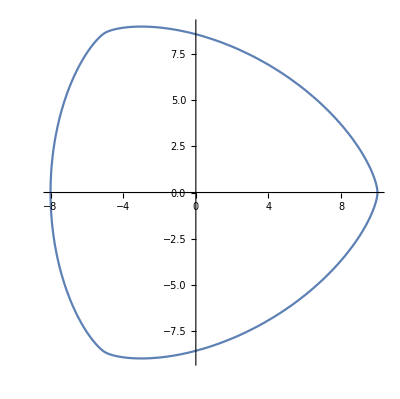

```mathematica
ParametricPlot[{9Cos[θ]+2Cos[2θ]-Cos[4θ],9Sin[θ]-2Sin[2θ]-Sin[4θ]},{θ,0,2π}]
```

```mathematica
RevolutionPlot3D[{15+9Cos[θ]+2Cos[2θ]-Cos[4θ],9Sin[θ]-2Sin[2θ]-Sin[4θ]},{θ,0,2π}]
```

-Graphics3D-

## 绘图样式

```mathematica
只是样式显示为管状，本质上还是曲线，是内摆线
```

```mathematica
ParametricPlot3D[{Cos[t]+Cos[2t],Sin[t]-Sin[2t],0},{t,0,2π},PlotStyle->Directive[Pink,Tube[0.2]]]
```

-Graphics3D-

## 参数方程表示

```mathematica
a=2;(*圆环半径*)
b=1;(*圆环的线半径*)
ParametricPlot3D[{(a+b Sin[v])Cos[u],(a+b Sin[v])Sin[u],b Cos[v]},{u,0,2π},{v,0,2π},
ImageSize->Medium]
```

-Graphics3D-

### 使用n=1的超椭圆

```mathematica
ParametricPlot3D[{Abs[Cos[t]]^2 Sign[Cos[t]](1+0.2 Abs[Cos[v]]^2 Sign[Cos[v]]),
Abs[Sin[t]]^2 Sign[Sin[t]](1+0.2 Abs[Cos[v]]^2 Sign[Cos[v]]),
0.2 Abs[Sin[v]]^2 Sign[Sin[v]]},{t,0,2Pi},{v,0,2Pi}]
```

-Graphics3D-

### 使用n=1的超椭圆作为路径，外摆线作为截面

```mathematica
Manipulate[
ParametricPlot3D[{Abs[Cos[t]]^2 Sign[Cos[t]](1+0.2(Cos[θ]+1/n Cos[n θ])),
Abs[Sin[t]]^2 Sign[Sin[t]](1+0.2(Cos[θ]+1/n Cos[n θ])),
0.2(Sin[θ]+1/n Sin[n θ])},{t,0,2Pi},{θ,0,2Pi},
ImageSize->Large],
{n,1,10,1}]
```

```mathematica
ParametricPlot3D[{(1+0.2Sin[2Cos[t]])Sin[u],(1+0.2Sin[2Cos[t]])Cos[u],0.2Sin[2Sin[t]]},{u,0,20},{t,0,2π}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{(1+0.2Sin[5Cos[t]])Sin[u],(1+0.2Sin[5Cos[t]])Cos[u],0.2Sin[2Sin[t]]},{u,0,20},{t,0,2π}]
```

-Graphics3D-

```mathematica
n=2;
ParametricPlot3D[{Abs[Cos[t]]^(2/n)Sign[Cos[t]](1+0.2 Abs[Cos[v]]^(2/n)Sign[Cos[v]]),
Abs[Sin[t]]^(2/n)Sign[Sin[t]](1+0.2 Abs[Cos[v]]^(2/n)Sign[Cos[v]]),
0.2 Abs[Sin[v]]^(2/n)Sign[Sin[v]]},{t,0,2Pi},{v,0,2Pi},
MaxRecursion->5]
```

-Graphics3D-

```mathematica
Animate[ParametricPlot3D[{Abs[Cos[t]]^0.5 Sign[Cos[t]](1+0.2 Abs[Cos[v]]^0.5 Sign[Cos[v]]),
Abs[Sin[t]]^0.5 Sign[Sin[t]](1+0.2 Abs[Cos[v]]^0.5 Sign[Cos[v]]),
0.2 Abs[Sin[v]]^0.5 Sign[Sin[v]]},{t,0,k},{v,0,2Pi},
PlotRange->1.5],{k,0.01,2π}]
```

### 好了，谢谢观看，欢迎留下您的评论，下期见。